# Half Rod, Albedo Problem, Isotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
-Graphics-

## Analytic solutions

### Half rod reflectance/albedo (R)

```mathematica
Clear[α,g];
halfrodalbedoisoscatter`R[α_]:=2(-α/2-√(1-α)+1)/α
```

```mathematica
Series[halfrodalbedoisoscatter`R[α],{α,0,5}]
```

α/4+α^2/8+(5 α^3)/64+(7 α^4)/128+(21 α^5)/512+O[α]^6

```mathematica
halfrodalbedoisoscatter`R[α_,n_]:=α^n 2 (-1)^n Binomial[1/2,n+1]
```

### Internal distribution, ‘radiance’

```mathematica
halfrodalbedoisoscatter`LR[x_,α_,Σt_]:=ⅇ^(-√(1-α) Σt x)
```

```mathematica
halfrodalbedoisoscatter`LL[x_,α_,Σt_]:=(α Exp[-Σt √(1-α)x])/(-α+2 √(1-α)+2)
```

### Fluence

```mathematica
halfrodalbedoisoscatter`ϕ[x_,α_,Σt_]:=halfrodalbedoisoscatter`LR[x,α,Σt]+halfrodalbedoisoscatter`LL[x,α,Σt]
```

### n-th collided fluence

```mathematica
halfrodalbedoisoscatter`ϕ[x_,α_,Σt_,n_]:=α^n(SeriesCoefficient[halfrodalbedoisoscatter`ϕ[x,A,Σt],{A,0,n}]/.A->α)
```

### Moments

```mathematica
halfrodalbedoisoscatter`ϕm[α_,Σt_,k_]:=(2 (1-α)^(-1-k/2) (-1+√(1-α)+α) Σt^(-1-k) Gamma[1+k])/α
```

Only accurate for n even

```mathematica
halfrodalbedoisoscatter`ϕm[α_,Σt_,k_,n_]:=α^n(2 (-1)^n Σt^(-1-k) Gamma[1+k] (-(2+n) Gamma[(1-k)/2]-((k+n) Binomial[-k/2,1+n]+2 (2+n) Binomial[-k/2,2+n]) Gamma[-1/2-k/2-n] Gamma[2+n]))/(Gamma[-1/2-k/2-n] Gamma[3+n])
```

## load MC data

```mathematica
halfrodalbedoisoscatter`ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
halfrodalbedoisoscatter`fs=FileNames["code/rod/halfrod/albedoProblem/data/halfrod_albedoproblem_isotropicscatter_exp*"];
```

```mathematica
halfrodalbedoisoscatter`index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
{α,Σt,data}];
halfrodalbedoisoscatter`simulations=halfrodalbedoisoscatter`index/@halfrodalbedoisoscatter`fs;
```

```mathematica
halfrodalbedoisoscatter`alphas=Union[#[[1]]&/@halfrodalbedoisoscatter`simulations]
```

{0.1,0.3,0.5,0.7,0.9,0.95,0.98,0.99,0.999}

```mathematica
halfrodalbedoisoscatter`muts=Union[#[[2]]&/@halfrodalbedoisoscatter`simulations]
```

{1,3}

```mathematica
halfrodalbedoisoscatter`numcollorders=halfrodalbedoisoscatter`simulations[[1]][[3]][[2,11]]
```

20

## Halfrod Albedo

```mathematica
MCalbedo[f_]:=Module[{data,α},
data=Import[f,"Table"];
α=data[[2,3]];
{α,data[[3,3]]}
]
```

```mathematica
MCalbedos=Table[MCalbedo[f],{f,halfrodalbedoisoscatter`fs}]
```

{{0.1,0.0262874},{0.1,0.0262874},{0.3,0.0888128},{0.3,0.0888128},{0.5,0.17156},{0.5,0.17156},{0.7,0.291991},{0.7,0.291991},{0.95,0.633904},{0.95,0.633904},{0.98,0.751703},{0.98,0.751703},{0.999,0.938793},{0.999,0.938793},{0.99,0.818082},{0.99,0.818082},{0.9,0.519448},{0.9,0.519448}}

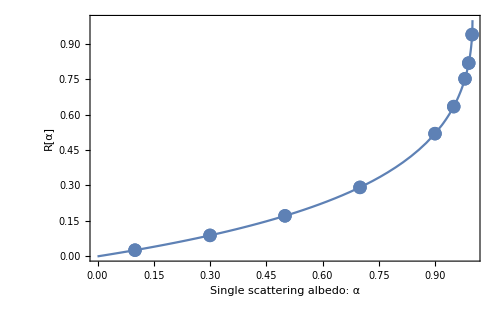

```mathematica
Clear[α];vizrodalbedoiso=Show[
Plot[halfrodalbedoisoscatter`R[c],{c,0,1}],
ListPlot[MCalbedos]
,Frame->True,ImageSize->500,FrameLabel->{{"R[α]",},{"Single scattering albedo: α","Total Reflectance/Albedo R(α): isotropically-scattering half rod"}}
]
```

### n-th collided albedo

```mathematica
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,Rs,ns,analytic,j,numcollorders},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
numcollorders=data[[2,11]];
Rs=N[{data[[5]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[halfrodalbedoisoscatter`R[α,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.95},halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts}]
```

## Compare Deterministic and MC

### Internal distribution

```mathematica
Clear[alpha,Σt];
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,maxx,dx,numcollorders,nummoments,pointsCL,plotpointsCL,pointsCR,plotpointsCR,plotpointsϕ,plotϕ,plotLL,plotLR},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];

pointsCL = data[[7]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=halfrodalbedoisoscatter`ppoints[pointsCL,dx,maxx,Σt];
pointsCR = data[[9]];
plotpointsCR=halfrodalbedoisoscatter`ppoints[pointsCR,dx,maxx,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=halfrodalbedoisoscatter`ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[halfrodalbedoisoscatter`ϕ[x,α,Σt],{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{"x","Semi-infinite rod, albedo problem, isotropic scattering, fluence ϕ[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}}
];

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[halfrodalbedoisoscatter`LL[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[halfrodalbedoisoscatter`ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{"x","Semi-infinite rod, albedo problem, isotropic scattering, L_-[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
];

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[halfrodalbedoisoscatter`LR[x,α,Σt],{x,0,maxx},PlotRange->All],
Plot[halfrodalbedoisoscatter`ϕ[x,α,Σt],{x,0,maxx},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{"x","Semi-infinite rod, albedo problem, isotropic scattering, L_+[x], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
];
Show[GraphicsGrid[{{plotϕ},{plotLL},{plotLR}}],ImageSize->500]
]
,
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.7},halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts}]
```

### N-th order Radiance/Angular flux

```mathematica
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,nthL,nthR,maxx,dx,numcollorders,LnR},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Clear[c,x];LnR=SeriesCoefficient[halfrodalbedoisoscatter`LR[x,c,Σt],{c,0,n}] α^n;
Show[
ListPlot[halfrodalbedoisoscatter`ppoints[nthR[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LnR,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, isotropic scattering, L_+[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.9},halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts},{{n,6},Range[If[NumberQ[halfrodalbedoisoscatter`numcollorders],halfrodalbedoisoscatter`numcollorders,1]]}]
```

### N-th order Fluence / scalar flux

```mathematica
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,maxx,dx,numcollorders,nthL,nthR,ϕn},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
maxx=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nthL=data[[13+numcollorders+1;;13+2numcollorders]];
nthR=data[[13+2 numcollorders+2;;-1]];

Clear[c];ϕn=SeriesCoefficient[halfrodalbedoisoscatter`ϕ[x,c,Σt],{c,0,n}] α^n;
Show[
ListPlot[halfrodalbedoisoscatter`ppoints[nthR[[n+1]]+nthL[[n+1]],dx,maxx,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕn,{x,0,maxx},PlotRange->All]
,Frame->True,
FrameLabel->{{SubPlus[L]["x|"<>ToString[n]],},{x,"Semi-Infinite Rod, albedo problem, isotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.9},halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts},{{n,6},Range[If[NumberQ[halfrodalbedoisoscatter`numcollorders],halfrodalbedoisoscatter`numcollorders,1]]}]
```

### Compare moments of ϕ

Divide these results, which are collision density moments, by Σt to produce radiance/fluence moments:

```mathematica
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,nummoments,ϕmoments,ks,analytic,j},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
nummoments=data[[2,13]];
ϕmoments=N[{data[[11]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[halfrodalbedoisoscatter`ϕm[α,Σt,k],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{α,halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts}]
```

### n-th collided moments of ϕ

```mathematica
Manipulate[
If[Length[halfrodalbedoisoscatter`simulations]>0,
Module[{data,ϕmoments,ks,analytic,j,nummoments},
data=SelectFirst[halfrodalbedoisoscatter`simulations,#[[1]]==α&&#[[2]]==Σt&][[3]];
nummoments=data[[2,13]];
ϕmoments=N[{data[[13+n]]}/Σt];
ks={Table[k,{k,0,nummoments-1}]};
analytic=Table[Quiet[N[halfrodalbedoisoscatter`ϕm[α,Σt,k,n]]],{k,ks}];
j=Join[ks,analytic,ϕmoments];
TableForm[
Join[{{"k","analytic","MC"}},Transpose[j]]
]
],
Text["Uh oh!  Couldn't find MC data.  Try to evaluate this entire notebook and ensure the data path is setup correctly."]
]
,{{α,0.7},halfrodalbedoisoscatter`alphas},{Σt,halfrodalbedoisoscatter`muts},{{n,4},Range[If[NumberQ[halfrodalbedoisoscatter`numcollorders],halfrodalbedoisoscatter`numcollorders,1]]}]
```